```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plot options for notebook

```mathematica
imgsize=400;
```

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30},ImageSize->imgsize}];
SetOptions[ListLinePlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->18},ImageSize->imgsize}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

# Basis functions for the Galton-Watson process

Setup

### Pick range for nu

```mathematica
m=30;
```

```mathematica
nuMin=0.1//N;
nuMax=3.0//N;
```

```mathematica
deltanu=(nuMax-nuMin)/(m-1)//N;
```

```mathematica
nuGrid=Table[i,{i,nuMin,nuMax,(nuMax-nuMin)/(m-1)}]//N;
```

### Delta function approximation

```mathematica
sigma=0.01;
delta[x_,y_]:=Exp[-(x-y)^2/(2*sigma^2)]/Sqrt[2*Pi*sigma^2];
```

### Set Max time T and increment Delta t

```mathematica
tMax=1.0;
deltat=0.05;
nTime=IntegerPart[tMax/deltat];
```

```mathematica
tGrid=Table[i,{i,0,tMax,deltat}];
```

### Reaction rates

```mathematica
kB=0.5;
kD=1.5;
```

Algorithm helper functions

### Interpolate f

```mathematica
interpolate[f_]:=Module[
{fTable},
fTable=Table[{nuMin+i*deltanu,f[[i+1]]},{i,0,m-1}];
Return[Interpolation[fTable,InterpolationOrder->1]];
];
```

```mathematica
interpolateSmoothed[f_]:=Module[
{fSmoothed,fTable},
fSmoothed=LowpassFilter[f,0.5];
fTable=Table[{{nuMin+i*deltanu},fSmoothed[[i+1]]},{i,0,m-1}];
Return[Interpolation[fTable]];
];
```

### Solve the diff eqs

```mathematica
eps=0.01;
perturb[nu_,nuVary_]:=Exp[-(nu-nuVary)^2/(2*eps^2)]/Sqrt[2.0*Pi*eps^2];
fPerturb[fInterp_,nu_,nuVary_,mag_]:=fInterp[nu]+mag*perturb[nu,nuVary];
```

```mathematica
generateNuTrajectoryPerturb[fInterp_,nu0_,nuVary_,mag_]:=Module[
{sol,maxTime,nuSt,iMax}
,
sol=Quiet[NDSolve[{
nu'[t]==fPerturb[fInterp,nu[t],nuVary,mag],
nu[0]==nu0,
WhenEvent[nu[t]>=nuMax,"StopIntegration"],
WhenEvent[nu[t]<=nuMin,"StopIntegration"]},
nu,{t,0,tMax}]][[1]];
maxTime=(nu/.sol/.InterpolatingFunction[{a_},__]:>a)[[2]];
nuSt=Table[(nu/.sol)[tVal],{tVal,0,maxTime,deltat}];
Return[{nuSt,Length[nuSt]}]
];
```

```mathematica
generateNuTrajectory[fInterp_,nu0_]:=generateNuTrajectoryPerturb[fInterp,nu0,0.0,0.0];
```

```mathematica
solveDEs[fInterp_,nu0_]:=Module[
{numag,rtrue,nuTrajSt,nuLengthSt,nuLength,tbl,tblinterp,tblder,firstKey,correctLength,deleteList,nutrue,lengthTest}
,
numag=0.001;

(* Store r - first level = time, second = pos to vary *)
rtrue=Association[];

(* Go through all nu to vary at *)
Do[

(* Solve for nu trajectory for different perturbations *)
nuTrajSt=Association[];
nuLengthSt=Association[];
Do[
{nuTrajSt[nuVaryMag],nuLengthSt[nuVaryMag]}=generateNuTrajectoryPerturb[fInterp,nu0,nuVary,nuVaryMag];
,{nuVaryMag,-numag,numag,numag}];

(* Max length *)
nuLength=Min[Values[nuLengthSt]];

(* Go through all times *)
Do[
tbl=Table[{nuVaryMag,nuTrajSt[nuVaryMag][[iTime]]},{nuVaryMag,-numag,numag,numag}];
tblinterp=Interpolation[tbl,InterpolationOrder->2];
tblder=Derivative[1][tblinterp];
If[!KeyExistsQ[rtrue,iTime],rtrue[iTime]=Association[];];
rtrue[iTime][nuVary]=tblder[0.0];
,{iTime,1,nuLength}];

,{nuVary,nuGrid}];

(* Cut elements the max time of rtrue as necessary, such that all nuVary exist at each time *)
firstKey=Keys[rtrue][[1]];
correctLength=Length[rtrue[firstKey]];
deleteList={};
Do[
If[
Length[rtrue[key]]!=correctLength,
deleteList=Append[deleteList,key];
];
,{key,Keys[rtrue]}];
rtrue=KeyDrop[rtrue,deleteList];

(* Solve for the true nu *)
{nutrue,lengthTest}=generateNuTrajectory[fInterp,nu0];
nuLength=Min[Length[rtrue],lengthTest];

Return[{rtrue,nutrue,nuLength}];
];
```

#### Test

```mathematica
Clear[fInterp];
fInterp[nu_]:=Sin[nu];
{rsol,nusol,nuLength}=solveDEs[fInterp,1.0];
```

```mathematica
Manipulate[ListLinePlot[rsol[i],PlotRange->{0,2}],{i,1,Length[rsol],1}]
```

ListLinePlot::lpn: rsol[1.] is not a list of numbers or pairs of numbers.

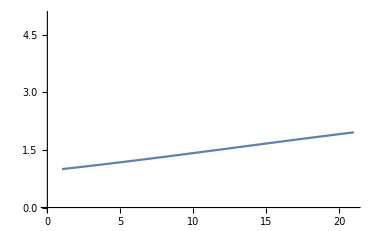

```mathematica
ListLinePlot[nusol,PlotRange->{0,5}]
```

### Average <n> from nu value

```mathematica
aveFromNu[nuTraj_]:=Table[1.0/(-1.0+Exp[nu]),{nu,nuTraj}];
```

### True average trajectory from the initial nu value

```mathematica
aveTrueFromNu0[nu0_,nTimeTraj_,deltat_]:=Module[
{aveTrue},
aveTrue=Association[];
aveTrue[0]=(1.0)/(-1.0+Exp[nu0]);
Do[
aveTrue[iTime]=aveTrue[iTime-1]+deltat*(kB-kD)*aveTrue[iTime-1];
,{iTime,1,nTimeTraj}];

Return[Values[aveTrue]]
];
```

### True solution

```mathematica
fTrue[nu_]:=(kD-kB)*(-Exp[-nu]+1);
```

### Solve true master equation prob dist

```mathematica
solveME[nmax_,nuIC_,krBirth_,krDeath_,nTimes_,dt_]:=Module[
{pSt}
,
(* Solution structure *)
pSt=Association[];
Do[
pSt[iTime]=Association[];
,{iTime,1,nTimes}];

(* IC *)
Do[
pSt[1][n]=fpt[n,nuIC];
,{n,0,nmax}];

(* Go *)
Do[
pSt[iTime][0]=pSt[iTime-1][0]+dt*krDeath*(pSt[iTime-1][1]);
Do[
pSt[iTime][n]=pSt[iTime-1][n]+dt*(krDeath*pSt[iTime-1][n+1]-krDeath*pSt[iTime-1][n]+krBirth*pSt[iTime-1][n-1]-krBirth*pSt[iTime-1][n]);
,{n,1,nmax-1}];
pSt[iTime][nmax]=pSt[iTime-1][nmax]+dt*(-krDeath*pSt[iTime-1][nmax]+krBirth*pSt[iTime-1][nmax-1]);
,{iTime,2,nTimes}];

Return[pSt];
];
```

### Boltz dist

```mathematica
fpt[n_,nu_]:=Exp[-(n+1)*nu]*(-1+Exp[nu]);
```

# Main algorithm v1: Integrate over IC in algorithm

Learning rate

```mathematica
nIter=40;
```

```mathematica
kLearningRate=0.02;
initialLearningRate=0.05;
finalLearningRate=0.01;
```

```mathematica
fMaxLearningRate[iter_]:=((finalLearningRate-initialLearningRate)/(Exp[-kLearningRate*(nIter-1)]-1))*(Exp[-kLearningRate(iter-1)]-1)+initialLearningRate;
```

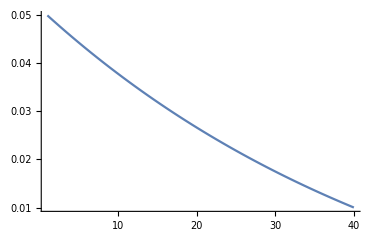

```mathematica
Plot[fMaxLearningRate[iter],{iter,1,nIter},PlotRange->{initialLearningRate,finalLearningRate}]
```

Run

```mathematica
(* Initialize F *)
(* Stored *)
(*f=f0;*)
(* True with noise *)
(*
noiseMag=0;
f=Table[fTrue[nuVal],{nuVal,nuGrid}]+RandomReal[noiseMag*{-1,1},m];
*)
(* Constant *)
f=ConstantArray[0.0,m];
(* Sin function *)
(*f=Table[Sin[nu],{nu,nuGrid}];*)

(* Store f *)
fSt=Association[];
fSt[0]=f;

(* Store action and updates for all ICs at all iterations *)
sIterSt=Association[];
dsdfIterSt=Association[];

Monitor[
Do[
(* Interpolate f *)
(*fInterp=interpolateSmoothed[f];*)
fInterp=interpolate[f];

(* Objective func update *)
dsdf=ConstantArray[0,m];

(* Store update for all ICs *)
dsdfSt=Association[];

(* Store action for all ICs *)
sSt=Association[];

(* Store r at all eta, times, varying at nuVary=2 *)
rEtaSt=Association[];

(* Store r for a single eta at all varys *)
rVarySt=Association[];

(* Go over all IC *)
Do[

(* Generate nu trajectory, solve pdes *)
(* Also get the number of steps before this traj runs off the domain *)
{rTraj,nuTraj,nTimeTraj}=solveDEs[fInterp,nu0Eval];

(* Store r, nu over all eta *)
rEtaSt[nu0Eval]=Table[rTraj[iTime][2.0],{iTime,1,nTimeTraj}];
nuEtaSt[nu0Eval]=nuTraj;
If[nu0Eval==2.0,
Do[
rVarySt[nuVary]=Table[rTraj[iTime][nuVary],{iTime,1,nTimeTraj}];
,{nuVary,nuGrid}];
];

(* Generate the trajectory of the average from nu *)
aveTraj=aveFromNu[nuTraj];

(* Generate the true average trajectory from the initial nu0Eval *)
aveTrajTrue=aveTrueFromNu0[nu0Eval,nTimeTraj,deltat];

(* Evaluate the objective function - table of nu to vary at *)
dsdflocal=ConstantArray[0.0,m];
Do[
dsdflocal+=deltat*(aveTrajTrue[[iTime]]-aveTraj[[iTime]])*Values[rTraj[iTime]];
,{iTime,1,nTimeTraj}];

(* Adjust magnitude such that the max is the learning rate *)
dsdflocal*=fMaxLearningRate[iIter]/Max[Abs[dsdflocal]];

(* Add to big update *)
dsdf+=dsdflocal;

(* Store *)
dsdfSt[nu0Eval]=dsdflocal;

(* Evaluate the ME prob dist *)
nmax=Max[IntegerPart[1.5*aveTraj[[1]]],1];
ptrue=solveME[nmax,nuTraj[[1]],kB,kD,nTimeTraj,deltat];

(* action, kl div *)
s=0.0;
Do[
dkl=0.0;
Do[
dkl+=ptrue[iTime][nVal]*Log[ptrue[iTime][nVal]/fpt[nVal,nuTraj[[iTime]]]]
,{nVal,0,nmax}];
s+=deltat*dkl;
,{iTime,1,nTimeTraj}];

sSt[nu0Eval]=s;

,{nu0Eval,nuGrid}];

(* Adjust magnitude such that the max is the learning rate *)
dsdf*=fMaxLearningRate[iIter]/Max[Abs[dsdf]];

(* Store the actions *)
sIterSt[iIter]=sSt;
dsdfIterSt[iIter]=dsdf;

(* Plot the action *)
If[iIter≠1,
fkey=Keys[sIterSt][[-1]];
pltsStacktbl1=Table[Table[sIterSt[k1][[k2]]-sIterSt[fkey][[k2]],{k1,Keys[sIterSt]}],{k2,1,m}];
pltsStacktbl2=Table[Table[pltsStacktbl1[[a1,a2]]/pltsStacktbl1[[a1,1]],{a2,1,Length[pltsStacktbl1[[a1]]]}],{a1,1,Length[pltsStacktbl1]}];
pltsStack=Show[
ListLinePlot[pltsStacktbl2,PlotStyle->LightGray,Frame->True,PlotLabel->"S (normalized)",FrameLabel->{"Iteration"},AspectRatio->1],
ListLinePlot[Mean[pltsStacktbl2],PlotStyle->Black,PlotRange->{-1,1}]
];
];

(* Plot dsdf *)
pltdsdfStacktbl=Table[Table[dsdfIterSt[k2][[k1]],{k2,Keys[dsdfIterSt]}],{k1,1,m}];
pltdsdfStack=Show[
ListLinePlot[pltdsdfStacktbl,PlotStyle->LightGray,Frame->True,PlotLabel->"δS/δF(ν)",FrameLabel->{"Iteration"},AspectRatio->1],
ListLinePlot[Mean[pltdsdfStacktbl],PlotStyle->Black]
];

(* Update the basis functions *)
f=Table[fInterp[nuVal],{nuVal,nuGrid}]-dsdf;

(* Store f *)
fSt[iIter]=f;

(* Plot *)
pltmax=1.5;
pltx={nuMin,nuMax};
plt=Show[
ListLinePlot[Transpose[{nuGrid,f}],PlotRange->{pltx,{0,pltmax}},AxesLabel->{"ν","F(ν)"},PlotStyle->{colors[[2]]}],
ListLinePlot[Transpose[{nuGrid,fSt[0]}],PlotRange->{pltx,{0,pltmax}},PlotStyle->{colors[[2]],Dashed}],
ListLinePlot[Table[{nuVal,fTrue[nuVal]},{nuVal,nuGrid}],PlotStyle->{colors[[1]],Dashed},PlotRange->{pltx,{0,pltmax}}]
,ImageSize->300
];

,{iIter,1,nIter}];
,
GraphicsGrid[{{
ProgressIndicator[iIter,{1,nIter}]
,
plt
}
,
{
pltsStack
,
pltdsdfStack
}}]
]
```

# Plots

Solution

```mathematica
pltmax=1.0;
pltx={nuMin,nuMax};
plt=ListLinePlot[{Table[{nuVal,fTrue[nuVal]},{nuVal,nuGrid}],Transpose[{nuGrid,f}],Transpose[{nuGrid,fSt[0]}]},PlotRange->{pltx,{-0.1,pltmax}},PlotLabel->"F(ν)",FrameLabel->{"ν"},Frame->True,PlotStyle->{{Darker[Red],Dashed},Darker[Blue],{Darker[Blue],Dashed}},PlotLegends->LineLegend[{"True","Final","Initial"},LabelStyle->{FontSize->18}]];
```

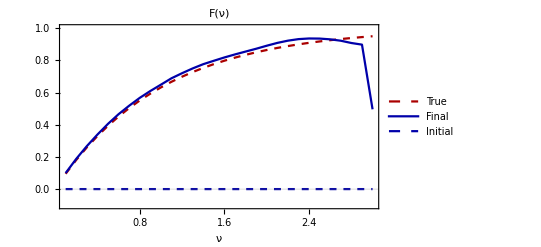

```mathematica
plt
```

```mathematica
plt1leg=LineLegend[{{Darker[Red],Dashed},Darker[Blue],{Darker[Blue],Dashed}},{"Analytic","Final","Initial"},LabelStyle->{FontSize->18}]
```

```mathematica
Export["../figures_gw_1d/sol_leg.pdf",plt1leg]
```

../figures_gw_1d/sol_leg.pdf

```mathematica
Export["../figures_gw_1d/sol.pdf",plt]
```

../figures_gw_1d/sol.pdf

Delta S / delta F over iterations

```mathematica
pltdsdfContourRange={-0.05,0.03};
pltdsdfContourtbl=Flatten[Table[{k1,nuGrid[[k2]],dsdfIterSt[k1][[k2]]},{k1,Keys[dsdfIterSt]},{k2,1,Length[dsdfIterSt[k1]]}],1];
pltdsdfContour=ListContourPlot[pltdsdfContourtbl,PlotLabel->"δS/δF(ν)",FrameLabel->{"Iteration","ν"},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}],ColorFunction->ColorData[{colorFunc,pltdsdfContourRange}],ColorFunctionScaling->False,PlotRange->pltdsdfContourRange];
```

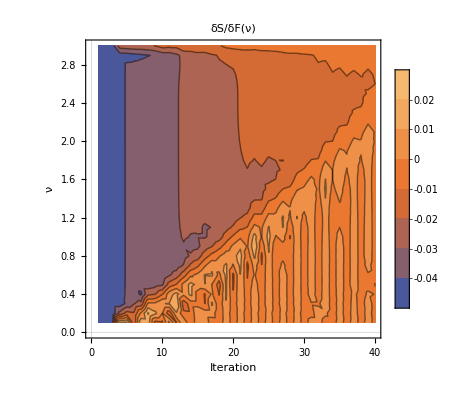

```mathematica
pltdsdfContour
```

```mathematica
Export["../figures_gw_1d/dsdf_contour.pdf",pltdsdfContour]
```

../figures_gw_1d/dsdf_contour.pdf

### Stack

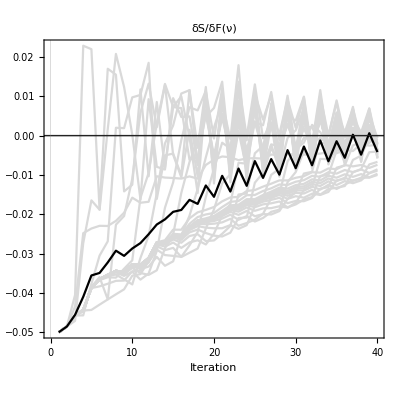

```mathematica
pltdsdfStacktbl=Table[Table[dsdfIterSt[k2][[k1]],{k2,Keys[dsdfIterSt]}],{k1,1,m}];
pltdsdfStack=Show[
ListLinePlot[pltdsdfStacktbl,PlotStyle->LightGray,Frame->True,PlotLabel->"δS/δF(ν)",FrameLabel->{"Iteration"},AspectRatio->1,BaseStyle->{FontSize->30}],
ListLinePlot[Mean[pltdsdfStacktbl],PlotStyle->Black],
Graphics@Line[{{-10,0},{50,0}}]
]
```

```mathematica
Export["../figures_gw_1d/dsdf_stack.pdf",pltdsdfStack]
```

../figures_gw_1d/dsdf_stack.pdf

### Slices

```mathematica
nuGrid[[20]]
```

2.

```mathematica
pltdsdfSlice1=ListLinePlot[Table[dsdfIterSt[k1][[20]],{k1,Keys[dsdfIterSt]}],PlotLabel->"δS/δF(ν=2.0)",AxesLabel->{"Iteration"}];
```

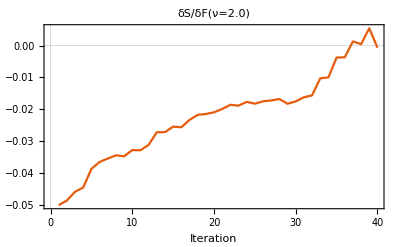

```mathematica
pltdsdfSlice1
```

S over iterations, from different IC

```mathematica
pltsContourRange={-0.1,0.5};
pltsContourtbl=Flatten[Table[{k1,k2,sIterSt[k1][k2]},{k1,Keys[sIterSt]},{k2,Keys[sIterSt[k1]]}],1];
pltsContour=ListContourPlot[pltsContourtbl,PlotLabel->"S",FrameLabel->{"Iteration","η"},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}],ColorFunction->ColorData[{colorFunc,pltsContourRange}],ColorFunctionScaling->False,PlotRange->{{0,40},{0,3},pltsContourRange}];
```

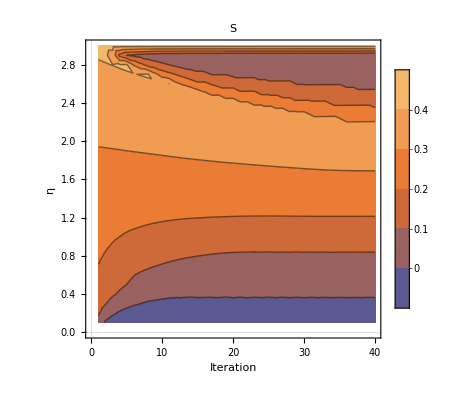

```mathematica
pltsContour
```

```mathematica
Export["../figures_gw_1d/s_contour.pdf",pltsContour]
```

../figures_gw_1d/s_contour.pdf

### Slices

```mathematica
nuGrid[[30]]
```

3.

```mathematica
pltsContourSlice1=ListLinePlot[Table[sIterSt[k1][[30]],{k1,Keys[sIterSt]}],PlotLabel->"S for η=2.5",AxesLabel->{"Iteration"}];
```

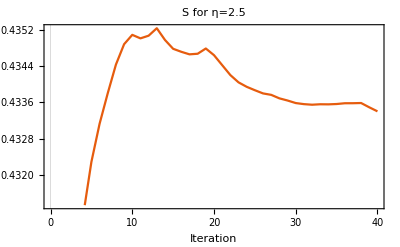

```mathematica
pltsContourSlice1
```

### Stacked, normalized slices

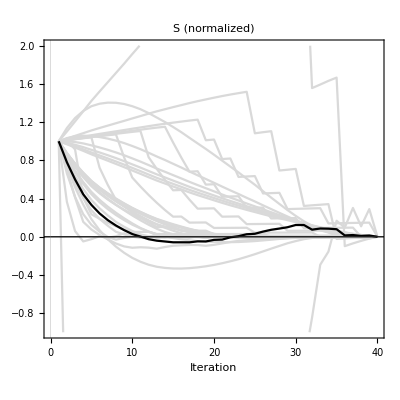

```mathematica
fkey=Keys[sIterSt][[-1]];
pltsStacktbl1=Table[Table[sIterSt[k1][[k2]]-sIterSt[fkey][[k2]],{k1,Keys[sIterSt]}],{k2,1,m}];
pltsStacktbl2=Table[Table[pltsStacktbl1[[a1,a2]]/pltsStacktbl1[[a1,1]],{a2,1,Length[pltsStacktbl1[[a1]]]}],{a1,1,Length[pltsStacktbl1]}];
pltsStack=Show[
ListLinePlot[pltsStacktbl2,PlotStyle->LightGray,Frame->True,PlotLabel->"S (normalized)",FrameLabel->{"Iteration"},AspectRatio->1,PlotRange->{-1,2},BaseStyle->{FontSize->30}],
ListLinePlot[Mean[pltsStacktbl2],PlotStyle->Black,PlotRange->{-1,2}],
Graphics@Line[{{-10,0},{50,0}}]
]
```

```mathematica
Export["../figures_gw_1d/s_stack.pdf",pltsStack]
```

../figures_gw_1d/s_stack.pdf

Variational term R

```mathematica
pltrRange={0.0,1.2};
pltrtbl=Flatten[Table[{tGrid[[k2]],k1,rEtaSt[k1][[k2]]},{k1,Keys[rEtaSt]},{k2,1,Length[rEtaSt[k1]]}],1];
pltrContour=ListContourPlot[pltrtbl,PlotLabel->"δν(t)/δF(ν=2.0)",FrameLabel->{"t","η"},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}],ColorFunction->ColorData[{colorFunc,pltrRange}],ColorFunctionScaling->False,PlotRange->pltrRange];
```

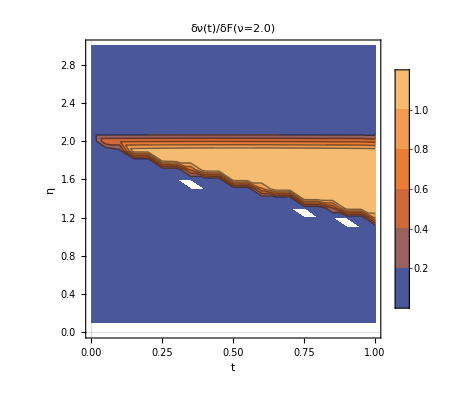

```mathematica
pltrContour
```

### Plot horizontal line at 2.0 for all times

```mathematica
plthoz=ListLinePlot[{{0.0,2.0},{1.0,2.0}},PlotStyle->{LightGray,Dashed}];
```

### Slice at eta=2.0

```mathematica
pltnu2p0=ListLinePlot[Transpose[{tGrid,nuEtaSt[2.0]}],PlotLabel->"ν(t) for η=2.0",AxesLabel->{"t"}];
```

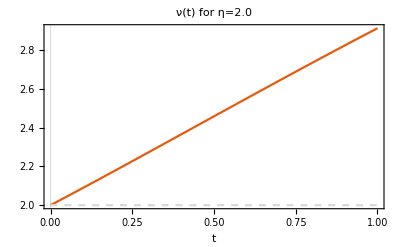

```mathematica
Show[pltnu2p0,plthoz]
```

```mathematica
pltrslice2p0tbl=Table[{tGrid[[k2]],rEtaSt[2.0][[k2]]},{k2,1,Length[rEtaSt[2.0]]}];
pltrslice2p0=ListLinePlot[pltrslice2p0tbl,PlotLabel->"δν(t)/δF(ν=2.0) for η=2.0",AxesLabel->{"t"},PlotLegends->Automatic];
```

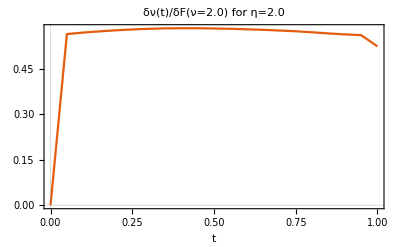

```mathematica
pltrslice2p0
```

### Slice at eta=1.5

```mathematica
pltnu1p5=ListLinePlot[Transpose[{tGrid,nuEtaSt[1.5]}],PlotLabel->"ν(t) for η=1.5",AxesLabel->{"t"}];
```

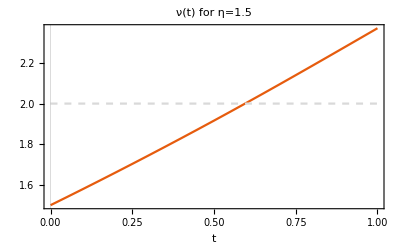

```mathematica
Show[pltnu1p5,plthoz]
```

```mathematica
pltrslice1p5tbl=Table[{tGrid[[k2]],rEtaSt[1.5][[k2]]},{k2,1,Length[rEtaSt[2.0]]}];
pltrslice1p5=ListLinePlot[pltrslice1p5tbl,PlotLabel->"δν(t)/δF(ν=2.0) for η=2.0",AxesLabel->{"t"},PlotLegends->Automatic];
```

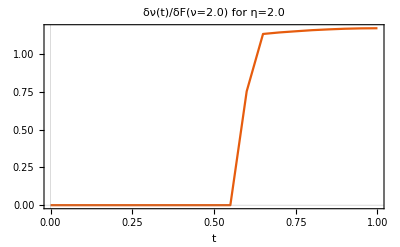

```mathematica
pltrslice1p5
```

### Stacked trajs

```mathematica
etaStack={1.5,1.6,1.7,1.8,1.9};
(*stackStyles={{Black,Dashed},{Black,Dotted},{Black,Dashed},{Black,Dotted},{Black,Dashed}};*)
stackStyles=Table[ColorData["AlpineColors",i/10.0],{i,1,5}];
```

```mathematica
(* determine vertical lines by intersections with trajectories of nu *)
pltvert={};
Do[
nuTrajTmp=Table[{tGrid[[k2]],nuEtaSt[etaS][[k2]]},{k2,1,Length[nuEtaSt[etaS]]}];
Do[
If[nuTrajTmp[[i+1,2]]>2.0&&nuTrajTmp[[i,2]]<2.0,
{tBelow,nuBelow}=nuTrajTmp[[i]];
{tAbove,nuAbove}=nuTrajTmp[[i+1]];
Break[];
];
,{i,1,Length[nuTrajTmp]-1}];

frac=(2.0-nuBelow)/(nuAbove-nuBelow);
tCross=tBelow+frac*(tAbove-tBelow);

AppendTo[pltvert,
ListLinePlot[{{tCross,-1.0},{tCross,4.0}},PlotStyle->{LightGray,Dashed}]
];

,{etaS,etaStack}];
```

```mathematica
pltrStacktbl=Table[Table[{tGrid[[k2]],rEtaSt[etaS][[k2]]},{k2,1,Length[rEtaSt[etaS]]}],{etaS,etaStack}];
pltrStack=Show[
ListLinePlot[pltrStacktbl,FrameLabel->{Automatic,"δν(t)/δF(ν=2.0)"},(*PlotLabel->"δν(t)/δF(ν=2.0)",*)(*FrameLabel->{"t"},*)Frame->True,PlotStyle->stackStyles,FrameTicksStyle->{Automatic,Directive[FontOpacity->0]}]
,
pltvert
,
ListLinePlot[pltrStacktbl,FrameLabel->{Automatic,"δν(t)/δF(ν=2.0)"},(*PlotLabel->"δν(t)/δF(ν=2.0)",*)(*FrameLabel->{"t"},*)Frame->True,PlotStyle->stackStyles,FrameTicksStyle->{Automatic,Directive[FontOpacity->0]}]
];
```

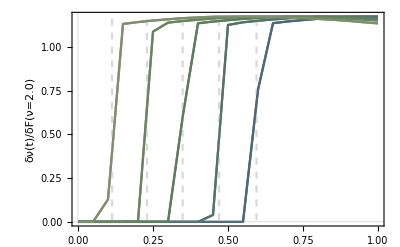

```mathematica
pltrStack
```

```mathematica
Export["../figures_gw_1d/r_stack.pdf",pltrStack]
```

../figures_gw_1d/r_stack.pdf

### Stack nu

```mathematica
pltnuStacktbl=Table[Table[{tGrid[[k2]],nuEtaSt[etaS][[k2]]},{k2,1,Length[nuEtaSt[etaS]]}],{etaS,etaStack}];
pltnuStack=Show[
ListLinePlot[pltnuStacktbl,(*PlotLabel->"ν(t)",*)FrameLabel->{"t","ν(t)"},PlotStyle->stackStyles,Frame->True],
plthoz,
pltvert,
ListLinePlot[pltnuStacktbl,(*PlotLabel->"ν(t)",*)FrameLabel->{"t","ν(t)"},PlotStyle->stackStyles,Frame->True]
];
```

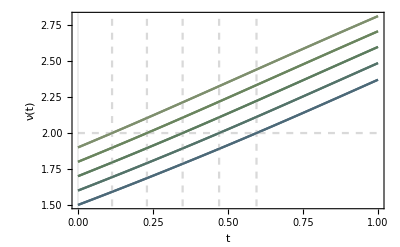

```mathematica
pltnuStack
```

```mathematica
Export["../figures_gw_1d/nu_stack.pdf",pltnuStack]
```

../figures_gw_1d/nu_stack.pdf